# Symbolic maths: Mathematica

Author: Nicholas Loutrel. Edited by Davide Gerosa.

Mathematica is a symbolic manipulation tool (also called "computer algebra"). I’m mostly a numerical person but, still, analytical progress is key. Go as far as you can in your problem with the analytics, and switch to numerics when it’s needed. 

For an example of my workflow, see https://arxiv.org/pdf/2304.04801
The appendices in that paper has some horrendous equations, that were all derived with Mathematica, exported to python (and also to latex to write the paper!), and integrated numerically from python.

## Introduction & Basic Operations

### Notebook Basics

Mathematica notebooks work in a near identical way to Jupyter/IPython notebooks. The notebooks contains cells, with each cell containing specific codes and commands, which are run by pressing ‘SHIFT + ENTER’.

```mathematica
2+2
```

4

‘In[#]’ are input cells, while ‘Out[#]’ are the output from the corresponding input cell.

Pressing ‘ENTER’ adds a new line within the input cell. Multiple expression can be evaluated per input cell using this method:

```mathematica
2+2
1+2
```

4

3

### Basic Arithmetic Operations

All basic math operations are specified with their corresponding symbols: + (addition), - (subtraction), * (multiplication), / (division), ^(exponentiation). Note the difference between Python and Mathematica for exponentiation!

```mathematica
8+13
```

21

```mathematica
21-8
```

13

```mathematica
2*2
```

4

```mathematica
4/2
```

2

```mathematica
2^2
```

4

Multiplication can also be achieved by adding in parentheses and/or spaces.

```mathematica
2(2)
```

4

But, remember order of operations!

```mathematica
2(1+1)
```

4

```mathematica
2 1+1
```

3

Mathematica contains a number of special symbols, which can be created by entering ‘Esc + Symbol/Key + Esc’. For example, the infinity symbol is obtained by entering ‘Esc  Inf  Esc’:

```mathematica
∞
```

∞

```mathematica
β
```

β

The multiplication symbol can take a special form using this method (input ‘Esc *  Esc’):

```mathematica
2×2
```

4

Other special formatting can be obtained through the ‘Ctrl + Key’ command. For example, division (‘Ctrl + /’) and exponentiation (‘Ctrl + ^’). There’s also a little pup-up panel at the top....

```mathematica
32/12
```

8/3

```mathematica
2^3
```

8

### Variables

Any letter entered as input is automatically treated as a variable. No need to tell Mathematica explicitly!

```mathematica
x
```

x

Notice the color of ‘x’ in the input cell (it’s blue, important in a moment).

Not all letters can be used as variables, as some are used for built-in functions or special mathematical symbols. For example, capital D is the function for differentiation (more on this later).

```mathematica
D[Cos[x]*x^2,x]
```

2 x Cos[x]-x^2 Sin[x]

Values can be assigned to variables using the ‘=’ symbol. Output for an input cell can be suppressed using the ‘;’ at the end of the cell.

```mathematica
x=2;
```

Now, notice again the color of ‘x’ from the input (both here and previously). It’s now black, which indicates visibly that it is already assigned a value. This also works if the letter is used internally for a function.

```mathematica
x
```

2

```mathematica
D
```

D

Variable names do not need to be single letters. They can be words ...

```mathematica
myVariable
```

myVariable

... or even Greek letters (input using ‘Esc + name_of_letter + Esc’).

```mathematica
α
```

α

But they cannot have any special character such as underscore (_), exclamation (!), etc. They also can’t start with numbers.

```mathematica
2myVariable
```

2 myVariable

```mathematica
3!
```

6

Mathematica just treats this as standard multiplication.

As a final note, be careful when assigning values to variables not use the double equals sign ‘==’. This is used for boolean statements:

```mathematica
x==2
```

True

If you inadvertently assign a variable a value, you can overwrite it by reassigning it’s value (if you intend for it to have one) ...

```mathematica
x=3;
x==3
```

True

... or you can use the ‘Clear’ function.

```mathematica
Clear[x]
```

Notice again that ‘x’ changed color to indicate it is unassigned any value.

### Substitution

Suppose you have the following expression ...

```mathematica
x^2+2x+1
```

1+2 x+x^2

... and you want to know what it’s value is without globally assigning a variable to ‘x.’ You can do this with substitutions, which are performed with the ‘/.{rule_to_sub}’ :

```mathematica
x^2+2x+1/.{x->2}
```

9

```mathematica
x
```

x

Notice again that ‘x’ is still unassigned. Substitutions generally apply their rules to the entirety of the cell, but do respect order of 
operations rules:

```mathematica
x^2+(2x+1)/.{x->2}
x^2+(2x+1/.{x->2})
```

9

5+x^2

Be careful when applying operations after the substitution on the input cell. Mathematica will complain:

```mathematica
x^2+(2x+1)/.{x->2}*2
```

ReplaceAll::reps: {2 (x→2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1+2 x+x^2/.{2 (x→2)}

Use parentheses if you need to do this:

```mathematica
(x^2+(2x+1)/.{x->2})*2
```

18

### Functions

All functions in Mathematica take inputs through brackets  [], not parentheses, which are only used for specifying parts of expressions. Functions you create follow the same naming rules as variables. To specify inputs, use the underscore, while to specify the functions itself, use ‘:=’:

```mathematica
f[x_]:=x^2+2x+1
```

```mathematica
f[2]
```

9

Notice again the color of the variable ‘x’, which is green in this case. This tells you that it is an internal/input variable to the function ‘f’. Also, ‘f’ is now assigned to be a function which takes ‘x’ as an input. It is possible to override the functions current assignment with ‘=’, so be 
careful!

```mathematica
f=2;
f==2
```

True

```mathematica
Clear[f]
f[x_]:=x^2+2x+1
```

To evaluate a function, simply add an input:

```mathematica
f[2]
f[y]
```

9

1+2 y+y^2

Note that functions respect the values of global variables:

```mathematica
a=2;
f[x_]:=x^2+a x+1
```

```mathematica
f[2]
f[y]
```

9

1+2 y+y^2

To specify more than one variable, use a comma for multiple inputs:

```mathematica
g[x_,y_,z_]:=x^2+y^2+z^2
```

```mathematica
g[1,2,3]
```

14

Functions can also be evaluated using the @ symbol and //. In these cases, the function should be understood as acting upon something. Note that // also applies to the entire input line like substitutions:

```mathematica
f[2]
```

9

```mathematica
f@2
```

9

```mathematica
2//f
```

9

```mathematica
1+1//f
```

9

Some built-in functions:

```mathematica
Cos[0]
Sin[0]
Sqrt[2]
Exp[-10]
Log[ⅇ]
Log10[10]
```

1

0

√2

1/ⅇ^10

1

1

### Numerical Evaluation & Precision

Consider the fraction:

```mathematica
2/3
```

2/3

Mathematic doesn’t give a decimal answer for it. This is because Mathematica can treat numbers with arbitrary floating point precision. To evaluate the fraction (or any number for that matter) to a decimal, use the ‘N’ function.

```mathematica
N[2/3]
N@(2/3)
2/3//N
```

0.666667

0.666667

0.666667

Note that the output only has a finite number of decimal points. You can change this by specify an additional option of ‘N’:

```mathematica
N[2/3,15]
```

0.666666666666667

```mathematica
N[2/3,100]
```

0.6666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667

Be careful though: if you give Mathematica decimals on number as an input, it will automatically evaluate the expression but only have finite precision.

```mathematica
2./3
```

0.666667

```mathematica
N[2./3.,15]
```

0.666667

### Help

To get help/documentation about built in Mathematica functions, use ‘?’:

```mathematica
?N
```

## Simplification

### Simplify & FullSimplify

The simplest built-in function for simplification is ‘Simplify’:

```mathematica
Simplify[x^2-2x+1]
```

(-1+x)^2

Another example, using trig functions and the ‘%’ symbol. ‘%’ tells Mathematica to take the output of the previous input and do something to it:

```mathematica
Sin[x]^2+Cos[x]^2
Simplify[%]
```

Cos[x]^2+Sin[x]^2

1

‘Simplify’ uses a variety of algebraic transformations to try to simplify an expression. But there are examples where it doesn’t simplify expressions in the desired way:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%]
```

√(x^2)

√(x^2)

The above example highlights a critical behavior of Mathematica, it assumes thing are as generic as possible. In this case, x could be a complex number. To fix this, apply assumptions:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x>0}]
%/.{x->2}
```

√(x^2)

x

2

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x<0}]
%/.{x->-2}
```

√(x^2)

-x

2

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x ∈ Reals}]
%/.{x->2}
%%/.{x->-2}
```

√(x^2)

Abs[x]

2

2

Note that the final expression varies depending on the assumptions, but they all give us the correct answer (Mathematica always assumes the square root is positive definite), with the final example being the most general. Note that substitution rules do not respect assumptions applied in previous simplifications steps. So careful!

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x<0}]
%/.{x->2}
```

√(x^2)

-x

-2

Another example using logarithms:

```mathematica
Simplify[Log[x]+Log[y]]
Simplify[Log[x]+Log[y],Assumptions->{x>0&&y>0}]
```

Log[x]+Log[y]

Log[x y]

When simplifying expressions with special functions, ‘Simplify’ may not be enough. Take for example, the Gamma function Γ(x), which for integer values reduces to the factorial Γ(n)=(n-1)!,  but generalizes to non-integer values. From the rules of factorials n Γ(n) = n!, and the generalization to arbitrary real numbers is x Γ(x) = Γ(x+1). But, ‘Simplify’ can’t do this:

```mathematica
Gamma[3]
(3-1)!
```

2

2

```mathematica
3*Gamma[3]
3!
```

6

6

```mathematica
2.1*Gamma[2.1]
Gamma[2.1+1]
```

2.19762

2.19762

```mathematica
Simplify[x Gamma[x]]
```

x Gamma[x]

In such cases, ‘FullSimplify’ may be used:

```mathematica
FullSimplify[x Gamma[x]]
```

Gamma[1+x]

‘FullSimplify’ applies a larger set of transformation rules than ‘Simplify’, but it is slower as a result (often much slower!), especially when dealing with very complicated expression. Two more examples highlighting the difference between ‘Simplify’ and ‘FullSimplify’:

1) Hyperbolic functions:

```mathematica
Simplify[Cosh[x]-Sinh[x]]
FullSimplify[Cosh[x]-Sinh[x]]
```

Cosh[x]-Sinh[x]

ⅇ^-x

2) √2+√3-√(5+2 √6)=0

```mathematica
Simplify[Sqrt[2]+Sqrt[3]-Sqrt[5+2Sqrt[6]]]
FullSimplify[Sqrt[2]+Sqrt[3]-Sqrt[5+2Sqrt[6]]]
```

√2+√3-√(5+2 √6)

0

‘FullSimplify’ may still need assumptions though:

```mathematica
FullSimplify[Sqrt[x^2]]
FullSimplify[Sqrt[x^2],Assumptions->{x>0}]
```

√(x^2)

x

### Expand & ExpandAll

Expressions involving polynomials can be expanded out using the ‘Expand’ function:

```mathematica
Expand[(x+1)^2(x-1)^2]
Expand[x(x^2+1)(x^3+3)]
```

1-2 x^2+x^4

3 x+3 x^3+x^4+x^6

‘Expand’ doesn’t operate within “subexpressions.” For example:

```mathematica
Expand[Sqrt[(1+x)^2]]
```

√((1+x)^2)

To expand the polynomial inside of the square root, use ‘ExpandAll’:

```mathematica
ExpandAll[Sqrt[(1+x)^2]]
```

√(1+2 x+x^2)

Similarly, ‘Expand’ only expands the numerator of expressions:

```mathematica
Expand[(x y+x^2+2 z^4)/(y+z)^4]
```

x^2/(y+z)^4+(x y)/(y+z)^4+(2 z^4)/(y+z)^4

Use ‘ExpandAll’ to expand both numerator and denominator:

```mathematica
ExpandAll[(x y+x^2+2 z^4)/(y+z)^4]
```

x^2/(y^4+4 y^3 z+6 y^2 z^2+4 y z^3+z^4)+(x y)/(y^4+4 y^3 z+6 y^2 z^2+4 y z^3+z^4)+(2 z^4)/(y^4+4 y^3 z+6 y^2 z^2+4 y z^3+z^4)

### PowerExpand & ComplexExpand

To expand powers in expressions, use ‘PowerExpand’:

```mathematica
PowerExpand[Sqrt[(1+x)^2]]
PowerExpand[Sqrt[x^2]]
PowerExpand[Sqrt[x y]]
PowerExpand[(-x)^(1/3)]
```

1+x

x

√x √y

(-1)^(1/3) x^(1/3)

Notice that with ‘PowerExpand’, we don’t need assumptions like we did with ‘Simplify’.
That is PowerExpand is not a mathematically safe transformation.

```mathematica
Simplify[Sqrt[x^2],Assumptions->{x>0}]
PowerExpand@Sqrt[x^2]
```

x

x

We can also expand assuming that all variables/expressions are complex using ‘ComplexExpand’:

```mathematica
ComplexExpand[(-1)^(1/3)]
```

1/2+(ⅈ √3)/2

Note that to input the imaginary unit, you can either type capital ‘I’ or ‘Esc + ii + Esc’:

```mathematica
I
```

ⅈ

```mathematica
ⅈ
```

ⅈ

```mathematica
ComplexExpand[Sin[x+I y]]
ComplexExpand[Sin[x+ⅈ y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

### Factoring Polynomials

Polynomials can be factored using the ‘Factor’ function:

```mathematica
Factor[x^2-y^2]
Factor[x^2-2x+1]
Factor[x^10-1]
```

(x-y) (x+y)

(-1+x)^2

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

### Manipulating Trig Expressions

Not all trig expressions can be simplified/manipulated with ‘Simplify’ and ‘Expand’.

```mathematica
Simplify[Sin[x]Cos[x]]
Simplify[Sin[x]^2]
Expand[Cos[3x]]
```

Cos[x] Sin[x]

Sin[x]^2

Cos[3 x]

For these, use ‘TrigReduce’ and ‘TrigExpand’:

```mathematica
TrigReduce[Sin[x]Cos[x]]
TrigReduce[Sin[x]^2]
TrigExpand[Cos[3x]]
```

1/2 Sin[2 x]

1/2 (1-Cos[2 x])

Cos[x]^3-3 Cos[x] Sin[x]^2

Generically, ‘TrigExpand’ takes functions of the form cos(n*x) or sin(n*x), and transforms them to forms contain [cos(x)]^n and [sin(x)]^n. ‘TrigReduce’ does the reverse of this.

```mathematica
TrigExpand[Sin[4x]]
TrigReduce[%]
```

4 Cos[x]^3 Sin[x]-4 Cos[x] Sin[x]^3

Sin[4 x]

Trig functions can also be converted to complex exponentials and vice versa, using ‘TrigToExp’ and ‘ExpToTrig’.

```mathematica
TrigToExp[Cos[3x]]
ExpToTrig[Exp[ⅈ x]]
```

1/2 ⅇ^(-3 ⅈ x)+1/2 ⅇ^(3 ⅈ x)

Cos[x]+ⅈ Sin[x]

### Collect

This is use to collect common terms.

```mathematica
Collect[(y+y^3 x)^10,y,Simplify]
```

y^10+10 x y^12+45 x^2 y^14+120 x^3 y^16+210 x^4 y^18+252 x^5 y^20+210 x^6 y^22+120 x^7 y^24+45 x^8 y^26+10 x^9 y^28+x^10 y^30

```mathematica
cl =CoefficientList[(y+y^3 x)^10,y]
```

{0,0,0,0,0,0,0,0,0,0,1,0,10 x,0,45 x^2,0,120 x^3,0,210 x^4,0,252 x^5,0,210 x^6,0,120 x^7,0,45 x^8,0,10 x^9,0,x^10}

You can access elements in lists with double brackets . Note Mathematica starts counting from 1, not 0!

```mathematica
cl[[1]]
```

0

```mathematica
cl[[31]]
```

x^10

## Solving Systems of Algebraic Equations

### Solving Algebraic Equations

```mathematica
Clear[a,b,c]
```

The general function to solve algebraic equations is “Solve”. The output is always a list of substitution rules, ensuring that variables you use do not get overwritten. If more than one solution is found, you can take only one using [[n]] brackets.

Quick exercise: do you understand the syntax x/.%[[1]]  used below?

```mathematica
sol = Solve[a x^2+b x+c==0,x]
x/.%[[1]]
(*x/.Flatten@%%
x/.%%%*)
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

(-b-√(b^2-4 a c))/(2 a)

“Solve” also works with numerical coefficients, and can find complex solutions.

```mathematica
Solve[4 x^2+2x+1==0,x]
Solve[x^5==1,x]
%//ComplexExpand
```

{{x→1/4 (-1-ⅈ √3)},{x→1/4 (-1+ⅈ √3)}}

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

{{x→1},{x→-1/4-(√5)/4-ⅈ √(5/8-(√5)/8)},{x→-1/4+(√5)/4+ⅈ √(5/8+(√5)/8)},{x→-1/4+(√5)/4-ⅈ √(5/8+(√5)/8)},{x→-1/4-(√5)/4+ⅈ √(5/8-(√5)/8)}}

“Solve” can also take inequalities and systems of equations.

```mathematica
Solve[4 x^2+2x-1==0 &&x>0,x]
Solve[{4 x^2+2x-1==0,x>0},x]
```

{{x→1/4 (-1+√5)}}

{{x→1/4 (-1+√5)}}

You can even specify the domain of any solutions.

```mathematica
Solve[x^5==1,x,Reals]
Solve[x^5==1,x,Integers]
Solve[x^5==1,x,Complexes]
Solve[x^5==1,x]
```

{{x→1}}

{{x→1}}

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

But “Solve” is not all powerful! It primarily deals with linear and polynomial equations.

```mathematica
Solve[1/10==x-Sin[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[1/10==x-Sin[x],x]

“Solve” (and Mathematica in general), can also be horribly obtuse! 
(I never fully understood these type of outputs; they’re given in terms of Root objects, see https://reference.wolfram.com/language/ref/Root.html )

```mathematica
Solve[P^2==a^3,a]
```

{{a→P^(2/3)},{a→-(-1)^(1/3) P^(2/3)},{a→(-1)^(2/3) P^(2/3)}}

```mathematica
Solve[P^2==a^3,a,Reals]
```

{{a→Root[-P^2+#1^3&,1]}}

There is also a numerical version of “Solve” called “NSolve”, for cases where you are only looking for approximate answers. “NSolve” has the same limitations as “Solve”.

```mathematica
Solve[x^10-8 x^7+3 x^4-1==0,x]
NSolve[x^10-8 x^7+3 x^4-1==0,x]
```

{{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

{{x→-0.982486-1.70311 ⅈ},{x→-0.982486+1.70311 ⅈ},{x→-0.65741},{x→-0.494251-0.696934 ⅈ},{x→-0.494251+0.696934 ⅈ},{x→0.0930051-0.675781 ⅈ},{x→0.0930051+0.675781 ⅈ},{x→0.728752-0.240197 ⅈ},{x→0.728752+0.240197 ⅈ},{x→1.96737}}

```mathematica
NSolve[0.1==x-Sin[x],x]
```

{{x→0.85375},{x→-0.411874+0.73018 ⅈ},{x→-7.5007+2.7813 ⅈ},{x→-13.9011+3.35919 ⅈ},{x→-20.2392+3.72161 ⅈ},{x→-26.555+3.98686 ⅈ},{x→-32.86+4.19626 ⅈ},{x→-39.159+4.36933 ⅈ},{x→-45.4542+4.51683 ⅈ},{x→-51.7469+4.64535 ⅈ},{x→-58.0378+4.75923 ⅈ},{x→-64.3273+4.86146 ⅈ},{x→-70.6159+4.95422 ⅈ},{x→-76.9037+5.0391 ⅈ},{x→-83.1908+5.11733 ⅈ},{x→-89.4775+5.1899 ⅈ}}

### FindRoot: A more powerful solver

“Solve” and “NSolve” are limited to special classes of algebraic equations where exact or approximate techniques works. But there are far more powerful numerical algorithms (Newton’s method, secant method, etc.) to solve equations. These are implemented in Mathematica using the “FindRoot” function. The downside to these methods is you have to feed “FindRoot” an estimate of where the answer is (this is a result of the numerical methods it uses).

(Honestly, if you need these kind of numerical work, you’re better off using scipy. Mathematica is amazing for symbolic manipulation, but numerical work is better done elsewhere)

```mathematica
FindRoot[x^2-1==0,{x,1.1}]
```

{x→1.}

A detour on plotting (for finding a good guess):

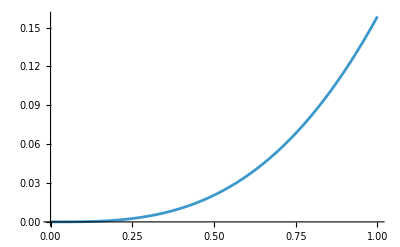

```mathematica
Plot[x-Sin[x],{x,0,1}]
```

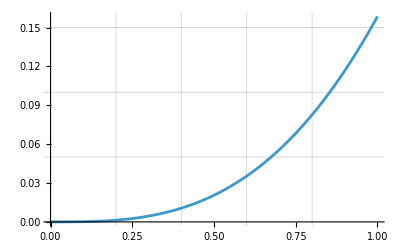

```mathematica
Plot[x-Sin[x],{x,0,1},GridLines->{{0.2,0.4,0.6,0.8},{0.05,0.1,0.15}}]
```

```mathematica
FindRoot[0.1==x-Sin[x],{x,0.8}]
(x-Sin[x]/.%)
%-0.1
```

{x→0.85375}

0.1

-2.77556×10^-17

## Calculus

### Differentiation

As mentioned at the beginning of this notebook, “D” corresponds to the built-in derivative functions within Mathematica.

```mathematica
D[x^2,x]
```

2 x

The function takes inputs in the form D[func_, vars_], the first of which is the function to differentiate and the second is the variable to differentiate with respect to. So this allows a very easy extension to multiple variables:

```mathematica
D[x y,y]
```

x

What if you want to take the second derivative? You might be tempted to do:

```mathematica
D[D[x^2,x],x]
```

2

BUT, you don’t need to do this! The following also works:

```mathematica
D[x^2,x,x]
D[x^2,{x,2}]
D[x y,x,y]
```

2

2

1

“D” can also be used to compute things like the gradient (vector) or Hessian/Jacobian (matrix):

```mathematica
D[x y,{{x,y}}] (*Gradient*)
D[x y,{{x,y},2}] (*Hessian/Jacobian*)
MatrixForm@%
```

{y,x}

{{0,1},{1,0}}

(0 | 1
1 | 0)

A few more examples, just to showcase how powerful this is.

```mathematica
Clear[f]
Clear[g]
D[x^n,x]
D[f[x]^n,x]
D[f[x]g[x],x]
D[f[x]/g[x],x]
D[a f[x]+b g[x],x]
```

n x^(-1+n)

n f[x]^(-1+n) f'[x]

g[x] f'[x]+f[x] g'[x]

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

a f'[x]+b g'[x]

Like many other things, there is a special symbol for the derivative operator that can be achieved using ‘Esc + pd + Esc’. To specify the variable to differentiate with respect to, use ‘Ctrl + Underscore’:

```mathematica
D[f[x], x]
```

f'[x]

```mathematica
D[f[y], y]
```

f'[y]

### Integration

The function for performing analytic integration in Mathematica is “Integrate”:

```mathematica
Integrate[x^2,x]
```

x^3/3

The above input/output shows an example of indefinite integration. “Integrate” has similar input structure to “D”:
D[func_, {vars_, n}]
Integrate[func_, {vars_, a, b}]
There are two differences though. The first is when specifying repeated integration. The following doesn’t work

```mathematica
Integrate[x^2,{x,2}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {x,2}.

Integrate[x^2,{x,2}]

... but the following does!

```mathematica
Integrate[x^2,x,x]
```

x^4/12

The reason is due to the second difference, which is that integrals can also be definite, and you can specify the limits of integration in the following way:

```mathematica
Integrate[x^2,{x,0,1}]
Integrate[Exp[x],{x,y,1}]
```

1/3

ⅇ-ⅇ^y

You can also perform integration with respect to multiple variables with a single command. For example, here is an example of the orthogonality of spherical harmonics:

```mathematica
Integrate[SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,-1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

1

0

“Integrate” is powerful and knows the results of many integral tables, for example
(∫_1)^∞dn n^-2 K_(2/3)(n z)K_(1/3)(n z)

```mathematica
Integrate[n^-2 BesselK[2/3,n z] BesselK[1/3,n z],{n,1,∞},Assumptions->{z>0&&z<1}]
```

1/(640 √3 z)π (-(1440 √π z^(2/3) HypergeometricPFQ[{-2/3,5/6},{1/3,2/3,4/3},z^2])/Gamma[1/6]+(4320 √π z^(4/3) HypergeometricPFQ[{-1/3,7/6},{2/3,4/3,5/3},z^2])/Gamma[-1/6]-243 z^4 HypergeometricPFQ[{1,1,5/2},{2,7/3,8/3,3},z^2]-40 (-8+9 z^2 (-7+4 EulerGamma+Log[729/16])+36 z^2 Log[z]))

### Series Expansions

Suppose you have a function and want to study it’s local behavior around a point (i.e. you need to compute it’s Taylor expansion/series). Mathematica has a function for this called “Series”:

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

The first input is always the function you desire to series expand, while the second is an array {} with structure {var, pt, order}. ‘var’ is the variable to series expand in, ‘pt’ is the value of the variable to expands around, and ‘order’ is the order of the expansion (highest power of ‘var’ in the series).

```mathematica
Clear[f]
Series[f[x],{x,x0,2}]
```

f[x0]+f'[x0] (x-x0)+1/2 f''[x0] (x-x0)^2+O[x-x0]^3

The output always has the O[x^n] symbol at the end of it, which indicates the remainder of the series expansion. From a formal theory perspective, this is fine, but you may notice Mathematica will not want to simplify/manipulate an expressions with this symbol. To get rid of it, apply the “Normal” function.

```mathematica
Normal@Series[f[x],{x,x0,2}]
Normal[Series[f[x],{x,x0,2}]]
Series[f[x],{x,x0,2}]//Normal
```

f[x0]+(x-x0) f'[x0]+1/2 (x-x0)^2 f''[x0]

f[x0]+(x-x0) f'[x0]+1/2 (x-x0)^2 f''[x0]

f[x0]+(x-x0) f'[x0]+1/2 (x-x0)^2 f''[x0]

“Series” can be useful for taking limits:

```mathematica
Sin[x]/x/.{x->0}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Series[Sin[x]/x,{x,0,3}]
Normal@%
%/.{x->0}
```

1-x^2/6+O[x]^4

1-x^2/6

1

Note, that “Series” can also compute asymptotic series:

```mathematica
Series[1/Sqrt[1+x^2],{x,∞,3}]
```

1/x-1/(2 x^3)+O[1/x]^4

### Numerical Integration

We covered “Integrate” already, but sometimes you may encounter complicated integrals that don’t have analytic solutions.

```mathematica
Integrate[1/x Cos[Log[x]/x],{x,0,1}]
```

∫_0^1 Cos[Log[x]/x]/x ⅆx

For these, you can use numerical integration via “NIntegrate”:

```mathematica
NIntegrate[1/x Cos[Log[x]/x],{x,0,1}]
```

0.323367

“NIntegrate” has much of the same functionality of “Integrate”, it just gives you numerical answers instead of analytic ones (so you can’t use it for indefinite integrals, sorry). Here’s a really pedantic integral that has an exact answer we can compare to the numerical one:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2}]
exact=Integrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2}]
%%-%//N
```

3.52549

4 ArcSinh[1]

-4.36428×10^-8

Pretty accurate, but we can do better by specify accuracy and precision tolerances. These are specified with the “AccuracyGoal” and “PrecisionGoal”, which have the following syntax:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},AccuracyGoal->13,PrecisionGoal->13]
exact-%//N
```

3.52549

-1.9984×10^-14

After each ‘->’ is a number which corresponds to desired accuracy/precision tolerance of order 10^-number. This can obviously be seen from the error computed above. The default for both of these is half “WorkingPrecision” (double precision for most applications), so the default is 7.

By default, Mathematica attempts to select the best numerical method to perform the integral out of all possible methods implemented (called the “Automatic” method). But, we can explicitly specify this with the “Method” option. For example, here’s the same integral above, but now using Monte Carlo integration:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},Method->"MonteCarlo",AccuracyGoal->13,PrecisionGoal->13]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 3.49008 and 0.0207346 for the integral and error estimates.

3.49008

Mathematica complains because the default options of its Monte Carlo routine are not sufficient to obtain the desired accuracy and precision tolerances. We can fix this by specifying options within the Monte Carlo method:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},Method->{"MonteCarlo",MaxPoints->10^6},AccuracyGoal->13,PrecisionGoal->13]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.52558 and 0.00598922 for the integral and error estimates.

3.52558

Obviously, this helps beat down the error in the Monte Carlo estimate, but is still not enough to reach the accuracy/precision tolerances. This is a result of the chosen method not being an optimal choice. Generally, when performing numerical integration (or numerically solving differential equations like we’ll see later), it’s best to let Mathematica choose the method for you, unless of course you know what you are doing.

The Monte Carlo method is also quite a bit slower than the method selected automatically by Mathematica. As a general rule, Mathematica is the slowest program you can pick for doing anything numerical. It’s much better to use numerical methods in something like Python. Mathematica’s numerical routines are just as powerful as those in other languages, it’s just painfully slow most of the time. The upside is that you can seamlessly transition from analytic calculations to numerical ones within Mathematica. No need to explicitly recode things! (Assuming you can deal with the slow speed).

## Differential Equations

### DSolve

Suppose you have the following differential equations: (∂_x)^2 y(x) + w^2 y(x) = 0. You can obtain the solution using the “DSolve” function:

```mathematica
DSolve[{y''[x]+w^2 y[x]==0},y[x],x]
```

{{y[x]→C[1] Cos[w x]+C[2] Sin[w x]}}

The output for “DSolve” is always in the form of a substitution rule. “DSolve” will also always give you the most general solution, with constants of integration unspecified. These can be fixed by specifying initial/boundary conditions:

```mathematica
DSolve[{y''[x]+w^2 y[x]==0,y[0]==1,y'[0]==0},y[x],x]
```

{{y[x]→Cos[w x]}}

The syntax for “DSolve”: DSolve[{eqn1, eqn2, ..., cond1, cond2, ...}, {funcs}, {vars}]

A few more examples:

```mathematica
(*1st Order ODE*)
DSolve[{y'[x]-y[x]==0,y[2]==1},y[x],x]
```

{{y[x]→ⅇ^(-2+x)}}

```mathematica
(*Bessel's equation*)
DSolve[{y''[x]+1/x y'[x]+(x^2-n^2)/x^2 y[x]==0},y[x],x]
```

{{y[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}}

```mathematica
(*2D wave equation*)
DSolve[{-1/c^2 D[z[t,x],{t,2}]+D[z[t,x],{x,2}]==0},z[t,x],{t,x},Assumptions->{c>0}]
```

{{z[t,x]→C[1][-c t+x]+C[2][c t+x]}}

```mathematica
(*Sturm-Liouville problem*)
DSolve[{y''[x]+w^2 y[x]==0,y[0]==0,y[π]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Sin[√(w^2) x], n∈ℤ&&n≥1&&w^2==n^2}, {0, True}}]}}

```mathematica
(*Coupled DEs*)
DSolve[{y'[t]+x[t] y[t]==0,x'[t]-y[t]x[t]==0},{x[t],y[t]},t]
```

{{y[t]→C[1]-(ⅇ^(t C[1]) C[1])/(ⅇ^(t C[1])-ⅇ^(C[1] C[2])),x[t]→(ⅇ^(t C[1]) C[1])/(ⅇ^(t C[1])-ⅇ^(C[1] C[2]))}}

### NDSolve

```mathematica
Clear[a]
```

Consider the Duffing oscillator: (∂_t)^2 y+2a ∂_t y+y+ϵ y^3=cos(w t). This is a common non-linear oscillator equation and does not have an exact (closed-form), analytic solution:

```mathematica
DSolve[{y''[t]+2a y'[t]+y[t]+ϵ y[t]^3==Cos[w t]},y[t],t]
```

DSolve[{y[t]+ϵ y[t]^3+2 a y'[t]+y''[t]==Cos[t w]},y[t],t]

But, it can be solved numerically. The numerical differential equation solver in Mathematica is called “NDSolve”. It has similar syntax to “DSolve”, with a few exceptions. First, you always have to specify initial/boundary conditions for the problem you want to solve numerically. Second, you have to give it a domain to integrate over instead of just the dependent variable. This is specified by {var, min, max} after the function you want to solve for in the syntax. Also, much like “NIntegrate”, you should specify accuracy and precision goals, and any other options you care for (if you know what you’re doing).

```mathematica
sol=NDSolve[{y''[t]-0.025y'[t]+y[t]+0.1 y[t]^3==Cos[2.1t],y[0]==1,y'[0]==0},y,{t,0,60},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

{{y→InterpolatingFunction[…]}}

Notice that the solution is given as an interpolating function, instead of a set of data points like you might find from numerical methods in Python/C/C++/etc. This is somewhat similar to the the dense-ouput functionality in some of scipy. Mathematica automatically interpolates the data it gets from running “NDSolve”. The data is stored so you can get it from the functions.

```mathematica
ynum[[0]]["ValuesOnGrid"]
Flatten@ynum[[0]]["Coordinates"]
ydat=Transpose[{%,%%}]
```

ValuesOnGrid

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[Coordinates].

Flatten[Coordinates]

{Flatten[Coordinates],ValuesOnGrid}

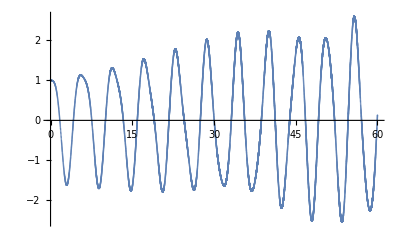

```mathematica
ListPlot[ydat]
```

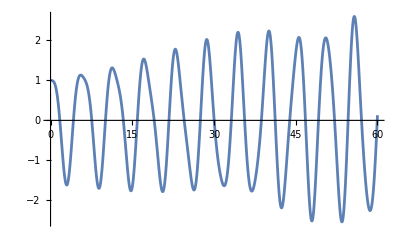

```mathematica
Plot[ynum,{t,0,60}]
```

Here is another (simpler) example using the “WhenEvent” event locator function to simulate a bouncing ball. The syntax for “WhenEvent” is WhenEvent[event, action].

{{y→InterpolatingFunction[…]}}

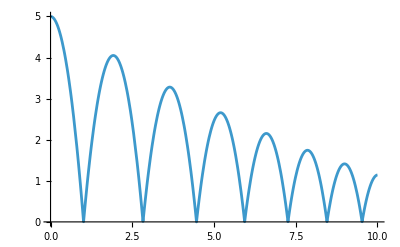

```mathematica
NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.9y'[t]]},y,{t,0,10}]
ynum=(y/.Flatten@%)[t];
Plot[ynum,{t,0,10}]
```

Much like “DSolve”, “NDSolve” is very versatile and can even solve PDEs numerically. The downside is that it has the same pitfalls as other numerical methods in Mathematica, i.e. they can be painfully slow.

## Export to latex

```mathematica
TeXForm@Cos[x]
```

\cos (x)

```mathematica
1/2 Log[577+408 √2]// TeXForm
```

\frac{1}{2} \log \left(577+408 \sqrt{2}\right)

```mathematica
1/2 Log[577+408 √2]// FortranForm
```

Log(577 + 408*Sqrt(2))/2.

To clear everything you' ve done so far ...

```mathematica
ClearAll["Global`*"]
```

```mathematica
MarcumQ[1,1,1]
```

1/2 (1+BesselI[0,1]/ⅇ)

## Exercises

For the exam complete two of these...

Q1: Find the first three roots of the Bessel function J_1(x).

Q2: Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.

Q3: Solve the equation  x ln(x) - 3 x + 10 = 6, both symbolically and numerically.

Q4: Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)
(bonus: solve it with scipy and check result and speed).  





...if you want more, here are some nice exercises: 
https://www.uv.es/calocla/BasicsAnswerKeyComments.pdf
https://www.programmingmathematica.com/uploads/2/4/7/6/24766996/epmexercisesandsolutions.pdf

```mathematica
sol = Solve[x+x^(2)==1,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
sol
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
sol[[1]]
```

{x→1/2 (-1-√5)}

```mathematica
x/.sol[[1]]
```

1/2 (-1-√5)